# Special Probability Distributions

Created in Mathematica by Sarah Sachs 🐺

## Binomial Distribution

Characteristics of a binomial experiment

Consists of a fixed number, say n, of independent trials.

Each trial may results in one of two possible outcomes, S or F.

P {success} = P(S) = p remains constant from trial to trial.

The random variable of interest is the binomial r.v. X = number of successes in n trials of the experiment.

binomial probability density function (p.d.f)

f(x) = b( x ; n p) = (n!)/(x!(n-x)!)p^xq^(n-x) for x = 0,1, ... n
			= 0, otherwise.
For the binomial r.v. X,  E[X] = n p, Var[X] = n p q.

```mathematica
Manipulate[DiscretePlot[PDF[BinomialDistribution[n,p],k],{k,10},PlotRange->All,PlotMarkers->Automatic],
{n,20,40,1},
{p,.1,.7,.25}]
```

### example

Five voters are randomly sampled with replacement from a community where 30% of the voters favor the bond issue. What is the probability that more than half in the sample will favor the issue?

## Hypergeometric Distribution

hypergeometric p.d.f

f(x) = h(x ; N, n, k) = P { x successes in a random sample of size n taken without replacement from a population of size N containing k successes}

f(x) =  h(x ; N, n, k) = ((k
x)(N -  k
n - x))/(N
n)

	   for x = 0, 1, ..., k 	if k < n or
		x= 0, 1, ..., n	 if n < k. 
For the hypergeometric r.v. X, E[X] = nk/N, and Var[X] =
	nk/N(1 - k/N)( (N-n)/(N-1)).

```mathematica
Manipulate[DiscretePlot[PDF[HypergeometricDistribution[n,50,100],k],{k,0,32},PlotRange->All],
{n,10,50,1}]
```

### example:

An enemy force is thought to be hiding in one of 20 locations. General Staff orders a search by picking a site at random, inspecting it, then picking the next site from the remaining 19 etc. After 15 sites have been inspected and the search is still not successful, is the General justified in believing that the enemy has left?

### example:

A complex of 10 missile sites is defined to be operational if at least 5 are functioning. An inspection consists of a random selection of four of the 10 sites. The complex is judged to be operational if at least 3 of the 4 inspected sites are functioning. If 4 of the 10 sites are actually functioning, what is the probability that the complex will be judged operational? 
	i.e. What is the probability that the complex will be judged to be operational when it is not?
	
This is an example of Lot acceptance sampling or hypothesis testing:
	Null hypothesis, H_0: Lot is acceptable ( or complex is operational)
	Alternative hypothesis, H_1: reject the lot (or complex flunks inspection)
	
	{Type I error} = {reject H_0| H_0 is true}
		e.g. reject lot when lot is good or judge complex nonoperational when complex is operational
		
	{Type II error} = {accept H_0 | H_1is true}
		e.g. accept lot with too many defectives or judge complex operational when only 4 missiles will fire.

### example

Lots of 40 components are called acceptable if they contain no more than 3 defectives. The procedure for sampling the lot is to select 5 components at random and to reject the lot if a defective is found. What is the probability that exactly 1 defective will be found if there are 4 in the entire lot?

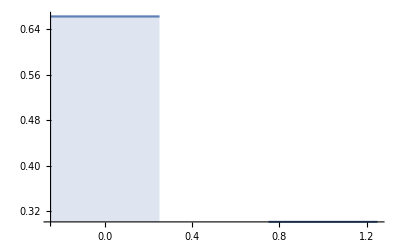

6545/18278

```mathematica
lot[n_] = HypergeometricDistribution[n,5,40];
DiscretePlot[PDF[lot[3],k],{k,0,1},ExtentSize->1/2]
Probability[x==1,x\[Distributed]lot[4]]
```

## Normal Distribution

If X ~ N(µ, σ^2) then X is continuous and the graph of the p.d.f. of X is a curve with the following properties:

bell-shaped

symmetric about the mean

asymptotic

```mathematica
Manipulate[Plot[PDF[NormalDistribution[μ,σ],x],{x,-6,6},Filling->Axis],
{μ,0,3,1},
{σ,1,10,.25}]
```

For any X ~ N(µ, σ^2), Z = (X-µ)/σ and Z ~ N(0,1) which is known as the standard normal distribution. The Z values are called standardized values or standard scores. 

The value of Z is actually the distance measured as the number of standard deviations that the chosen value of X is from its mean. For any normal distribution (i.e. regardless of its mean and standard deviation), the area under the curve of the p.d.f will always be the same for any particular number of standard deviations from the mean. For example, any value that is 2 standard deviations above its mean, (i.e. Z = 2), the area under the p.d.f. below or to the left of that value is 0.9772. This area is also the value of the c.d.f. for the standard normal at 2, i.e F_Z(2) = 0.9772

NOTE: The normal distribution describes probabilities for a continuous r.v. However, it is also sometimes used to approximate probabilities for certain discrete distributions, such as the binomial, negative binomial and Poisson distributions.

## Multinomial Distribution:

### If a given trial may result in one of k possible outcomes, E_I, E_2, ..., E_k, with probability p_1, p_2, ..., p_k, then the probability distribution of the random variables, X_I, X_2, ..., X_k, representing the number of occurrences of E_I, E_2, ..., E_k, in n independent trials is:

multinomial p.d.f.

f( X_I, X_2, ..., X_k;  n,  p_1,  p_2, ..., p_k) = (n!)/(X_I!,X_2!,...,X_k!)p_1^x_1p_2^x_2... p_k^x
Where ∑_(i=1)^k x_i= n and ∑_(i=1)^k p_k= 1. 

Since the multinomial is a joint p.d.f. for k random variables, it is also called a multivariate distribution. The binomial and hypergeometric distributions are univariate.

```mathematica
Manipulate[DiscretePlot3D[PDF[MultinomialDistribution[n,{0.6,0.4}],{x,y}],{y,0,n},{x,0,n},ExtentSize->0.5],{n,3,6,1}]
```

### example:

Consider rolling a pair of dice 6 times.  What is the probability of obtaining a 7 or 11 twice, a double once, and any other combinations 3 times?

## Negative binomial:

### If repeated independent trials can result in success with probability p and failure otherwise, the probability distribution of the random variable X, the number of trials until the k^thsuccess is:

negative binomial p.d.f.

f( x ) = b*( x ; k, p)  =  (x - 1
k - 1)  p^kq^(x-k)
for x = k, k+1, ... etc. 

For a negative binomial r.v., E[X] = k/p , Var[X] = k q / p^2 
A special case of the negative binomial is when k=1, this particular negative binomial is also called a geometric distribution.

geometric p.d.f.

f(x) = b * (x ; 1, p ) = p q^(x-1)

```mathematica
Manipulate[DiscretePlot[PDF[NegativeBinomialDistribution[2,p],k],{k,25},PlotMarkers->Automatic],{p,0.1,0.3,0.25}]
```

#### example:

To meet his yearly quota, a manager must sell 750 units.
(a) If his success rate is one in ten trials, what is the expected number of trials in order for him to meet his quota?

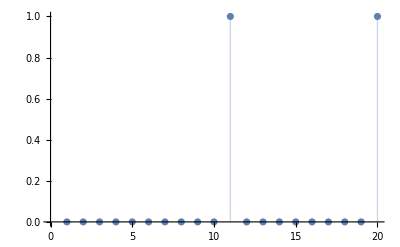

0.111111

```mathematica
RandomVariate[GeometricDistribution[.9],20];
ListPlot[%,Filling->Axis]
Mean[GeometricDistribution[.9]]
```

(b) If he has 20 people working for him and each independently can make 300 trials, what is the probability that he will achieve his quota? (assume constant success rate of 1/10 across all workers)

To increase his probability of making quota, the manager invests in an ad campaign designed to increase his success rate to one in seven. 
(c) How will this revised success rate effect his chances?

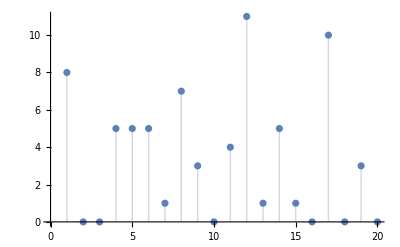

2.33333

```mathematica
RandomVariate[GeometricDistribution[0.3],20];
ListPlot[%,Filling->Axis]
Mean[GeometricDistribution[0.3]]
```

## Poisson Distribution

Characteristics of a Poisson Process

The number of occurrences in one interval of time ( or space ) is unaffected by the number of occurrences in any other nonoverlapping interval of time ( or space).

The expected number of occurrences over any interval of time ( or space ) is proportional to the size of the interval of time ( or space )

Events cannot occur simultaneously. [i.e. there is an interval of time ( or space ) sufficiently small that the probability of more than one occurrence in that interval is negligible.]

The random variable X, defined as the number of occurrences in a specified interval of time ( or space ) in a Poisson process, has the following p.d.f.

Poisson p.d.f.

f(x) = (e^-λ λ^x)/(x!) for x = 0, 1, 2, ... etc.
Where e = 2.71828.... (the base of the natural logarithm) and λ = the average number of occurrences for a specified interval of time ( or space ).

```mathematica
Clear[n];
Manipulate[DiscretePlot[PDF[PoissonDistribution[n],k],{k,0,20},PlotRange->All,PlotMarkers->Automatic],
{n,5,10}]
```

#### examples of Poisson r.v.’s:

number of flaws in a yard of fabric,

number of vacancies on the Supreme Court per year

number typing errors per page

number of days school is closed due to snowstorms

## Exponential Distribution

Consider a continuous r.v. T such that T measures the length of time between successive occurences of an event in a Poisson process. What is Pr {T > t} ?

P { T > t } = Pr { 0 occurrences in time t }

= Pr{ X = 0, in time t }

= ((e^-λt(λt))^0)/(0!)

= e^-λt

Note: in this case, λ represents the average number of occurrences in one unit of time. Therefore, λt  represents the average number of occurrences in time t.

Therefore: Pr { T < t } = 1 - P { T > t } = 1 - e^-λt.

If we let β = 1/λor λ = 1/β, then
	Pr { T ≤ t } = F(t) = 1 - e^(-t/β)

The random variable T has an exponential distribution with parameter β or mean of β, i.e. E[T] = β, also Var [T] = β^2.

The p.d.f. of the random variable T having an exponential distribution is

exponential p.d.f.

f(t) = 1/β e^(-t/β)	    for t ≥ 0, β > 0 .

To find probabilities associated with the random variable T, the corresponding area under the curve of the p.d.f. must be found. This may be accomplished by integrating the p.d.f. of T over the appropriate range.

Pr { T ≤ t } = ∫_(-∞)^t f(t)ⅆt

```mathematica
Manipulate[Plot[PDF[ExponentialDistribution[λ],x],{x,0,3},Filling->Axis,PlotRange->All],
{λ,1/2,3,.5}]
```

```mathematica
,
```

However, for those who have not had a course in calculus, areas can easily be found using the cumulative distribution function for T, i.e. the c.d.f. of T, F(t).

exponential c.d.f.

F(t) = Pr{ T ≤ t } = 1 - e^(-t/β)= 1 - e^-λt

```mathematica
Manipulate[Plot[CDF[ExponentialDistribution[λ],x],{x,0,4},Filling->Axis],
{λ,1/2,3,.5}]
```

## Practice Examples

In a study on “How Important Is Computer Service In Retail Branch Banking?” (Authored by Maggard and S. Globerson and reported in The Proceeding of the Decision Sciences Institute, 19 ... .. 906-8), a survey of over 50 branch bank managers revealed that an “acceptable” average waiting time for a customer to see a teller ranged from a low of .75 minute to a high of 10 minutes. Suppose that a certain manager believes that if the mean number of customers arriving over a 10-minute interval is a Poisson random variable with a mean of 3, then the average waiting time for a customer will be acceptable. What percentage of the time will the number of arrivals during a 10- minute interval exceed three, assuming the manager’s belief is correct?

```mathematica
N[1-CDF[PoissonDistribution[3],3],4]
```

0.3528

A salesperson has 15 major accounts. Eight of those accounts were sent the wrong billing last month (they were billed too much by the accountant). The salesperson wants to call her accounts to explain what happened, but she only has time to call 10 of them before quitting time (assume a call to a wrongly billed account takes just as long as a call to one with correct billing). If she selects accounts and calls them randomly, what is the probability that she will reach 6 of the 8 she wants to contact?

```mathematica
N[PDF[HypergeometricDistribution[10,8,15],6],4]
```

0.3263

A Bell’s Root Beer, Inc., soft-drink-dispensing machine has been reset so that it dispenses an amount that results in a cup overflow on only 1% of the 12- ounce cups that are used. The amount dispensed has a standard deviation of 1 ounce and is normally distributed. What is the new setting for the mean amount of soft drink that is dispensed?

Solve for the mean using the formula z=(x - µ)/σ

```mathematica
µ = 12-(2.32)*(1)
```

9.68

Solve for CDF

```mathematica
CDF[NormalDistribution[µ,1],12]
```

0.98983

A work study program was developed with a university and several industries in the surrounding community. Students were to work with industrial sociologists during a three-month internship. Equal numbers of students from the university were sent to a chemical, a textile, and a pharmaceutical industry. Students completing the program were classified according to the industry in which they interned. A random sample of twelve of the many students who completed the program was taken. What is the probability that five of the students interned in the chemical industry, and the rest of them interned in some other industry?

```mathematica
N[PDF[BinomialDistribution[12,1/3],5],4]
```

0.1908

In order to obtain cost savings, a company is considering offering an early retirement incentive for its older management personnel. The consulting firm that designed the early retirement program has found that approximately 22% of the employees qualifying for the program will select early retirement during the first year of eligibility. Assume that the company offers the early retirement program to 10 of its management personnel. What is the probability that at least 3  but no more than 5 will elect early retirement in the first year?

```mathematica
PDF[BinomialDistribution[10,.22],3]+PDF[BinomialDistribution[10,0.22],4]+PDF[BinomialDistribution[10,.22],5]
```

0.372726

The GM production department has installed a new spray machine to paint automobile doors. As is common with most spray guns, unsightly blemishes often appear because of improper mixture or other problems. A worker counted the number of blemishes on each door. Most doors had no blemishes, a few had one, a very few had two and so on. The average number was 0.5 blemishes per door. The distribution of blemishes followed the Poisson distribution. What is the probability that exactly two doors in a random sample of ten doors will have blemishes?

```mathematica
PDF[PoissonDistribution[0.5],2]
```

0.0758163

Over a long period of time in a large multinational corporation, 10% of all sales trainees are rated as outstanding, 75% as excellent/good, 10% as satisfactory, and 5% as unsatisfactory. Ten employees are randomly selected. What is the probability that two are rated as outstanding, 4 are rated as excellent/good and three are rated as satisfactory?

```mathematica
PDF[MultinomialDistribution[10,{0.1,0.75,0.1,0.05}],{2,4,3,1}]
```

0.00199336

A new technique, balloon angioplasty, is being widely used to open clogged heart valves and vessels. The balloon is inserted via a catheter and is inflated, opening the vessel; thus no surgery is required. Left untreated, 50% of the people with heart valve disease die within about two years. If experience with this technique suggests that approximately 70% live for more than two years, would the next five patients of the patients treated with balloon angioplasty at a hospital constitute a binomial with n = 5 and p = .70?

The trials are not identical from patient to patient, so the binomial distribution cannot be used.

In a batch of 20 bottles of their product the Restin Chemical Company knows that 10 bottles were contaminated. Assume that these 10 bottles were spread randomly through the batch. Restin’s best customer was recently sent 6 bottles from this batch and claims that 4 of the bottles were contaminated. Your boss would like to know the probability that this could happen.

```mathematica
N[PDF[HypergeometricDistribution[10,10,20],4],4]
```

0.2387

The World Series terminates when one team wins its fourth game. If the two teams are evenly matched, that is, if the probability that either team will win anyone game is .5, what is the probability that the series will terminate at the end of the fourth game?

```mathematica
PDF[BinomialDistribution[4,0.5],4]
```

0.0625

A door-to-door salesperson for Valley Products has a 20% sales success rate. Find the expected number of calls (assume these calls results are independent of one another) this person will have to make in order to make five sales.

A negative distribution using the expected value formula E(x) = k/p = 5/0.2 = 25

k = successes, p = probability

The number of paint blisters produced by an automated painting process at Associated Industries is Poisson distributed with a mean rate of .06 blisters per square foot. The process is about to be used to paint an item that measures 9 by 15 feet. What is the probability that the first 12 to 18 square feet will be without blisters?

For 12 sqft

mean = 0.06 blisters/sqft * 12 sqft = 0.72 blisters Solving for 0 blisters we get ((e^-0.72) (0.72^0))/0! = 0.4867

For 18 sq ft
mean = 0.06 blisters/sqft * 18 sqft = 1.08 blisters Solving for 0 blisters we get ((e^-1.08) (1.08^0))/0! = 0.3395

```mathematica
twelve = PDF[PoissonDistribution[.72],0];
eighteen=PDF[PoissonDistribution[1.08],0];
twelve - eighteen
```

0.147157

A soup company markets eight varieties of homemade soup throughout the Eastern states. The standard-sized soup can holds a maximum of 11 ounces, while the label on each can advertises contents of 10.75 ounces. The extra .25 ounces is to allow for the possibility of the automatic filling machine placing more soup than the company actually wants in a can. Past experience shows that the number of ounces placed in a can is approximately normally distributed, with a mean of 10.75 ounces and a standard deviation of .1 ounce. What is the probability that the machine will attempt to place more than 11 ounces in a can, causing an overflow to occur?

```mathematica
1-CDF[NormalDistribution[10.75,0.1],11]
```

0.00620967

A college basketball coach has 12 players on his roster. Eight of the players are receiving basketball scholarships, and four are not. Recently the team has been losing most of their games. The coach decided to draw the names of 5 players out of a hat and designate them as the starting lineup. What is the probability that four of the five players selected are on scholarship?

```mathematica
N[PDF[HypergeometricDistribution[5,5,12],4],6]
```

0.0441919